### Start choosing the example:

```mathematica
t=12;
beta = 0;
A = 0.2;
g[x]
```

Log[x]

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,1,0},{0,0,1,1},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
a[j_,edge_]:=
Which[
edge === 1->3 || edge === 2->4, j/100,
edge === 1->2 || edge === 3->4, 45,
edge === 2->3, 90000000,
True, 0
]
```

```mathematica
MFGEquations=DataToEquations[Data/.{I1->4000,U1->0}];//Timing
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

DataToEquations: The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.090078 seconds to reduce the critical congestion case with NewReduce!
The system is j641==2000&&j644==2000&&jt654==0&&jt660==0&&jt667==2000&&jt670==0&&jt674==0&&u682==2000&&u684==4000

DataToEquations: Critical congestion solved.

DataToEquations: Minimal Time? 
   1 for yes.

DataToEquations: Done.

{0.179073,Null}

```mathematica
EqMinimalTime=And@@(MapThread[(#1==#2)&,{MFGEquations["Nlhs"],MFGEquations["MinimalTimeRhs"]}]);
EqMinimalTime
```

j640-j647-u678+u685==-45+j640-j647&&j641-j648-u679+u686==j641-j648+1/100 (-j641+j648)&&j642-j649-u680+u687==-90000000+j642-j649&&j643-j650-u681+u688==j643-j650+1/100 (-j643+j650)&&j644-j651-u682+u689==-45+j644-j651

```mathematica
MFGEquations["uvars"]
```

<|{1,1->2}→u548,{1,1->3}→u549,{2,2->3}→u550,{2,2->4}→u551,{3,3->4}→u552,{4,4->ex509}→u553,{en508,en508->1}→u554,{2,1->2}→u555,{3,1->3}→u556,{3,2->3}→u557,{4,2->4}→u558,{4,3->4}→u559,{ex509,4->ex509}→u560,{1,en508->1}→u561|>

```mathematica
{mtsys,mtrules}=FixedPoint[EqEliminatorX,{MFGEquations["EqAllAll"]&&EqMinimalTime,{}}];
{mtsys,mtrules}=FixedPoint[EqEliminatorX,{NewReduce[mtsys],mtrules}];
```

```mathematica
mtrules
```

<|j640→0,j642→0,j643→9000004500,j645→4000,j646→4000,j647→9000000500,j648→0,j649→18000005000,j650→0,j651→9000000500,j652→0,j653→0,jt655→0,jt656→0,jt657→0,jt658→0,jt659→4000,jt661→0,jt662→9000000500,jt663→9000004500,jt664→0,jt665→0,jt666→9000004500,jt668→0,jt669→0,jt671→9000000500,jt672→9000000500,jt673→4000,jt675→0,jt676→0,jt677→0,u678→90000090,u679→90000090,u680→90000045,u681→90000045,u683→0,u685→90000045,u686→45,u687→45,u688→0,u689→0,u690→0,u691→90000090,j641→9000004500,j644→0,jt654→9000000500,jt660→0,jt667→0,jt670→0,jt674→0,u682→45,u684→90000090|>

```mathematica
MFGEquations["jvars"]/.mtrules
```

<|{2,1->2}→0,{3,1->3}→9000004500,{3,2->3}→0,{4,2->4}→9000004500,{4,3->4}→0,{ex639,4->ex639}→4000,{1,en638->1}→4000,{1,1->2}→9000000500,{1,1->3}→0,{2,2->3}→18000005000,{2,2->4}→0,{3,3->4}→9000000500,{4,4->ex639}→0,{en638,en638->1}→0|>

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j640→2000,j641→2000,j642→0,j643→2000,j644→2000,j645→4000,j646→4000,j647→0,j648→0,j649→0,j650→0,j651→0,j652→0,j653→0,jt654→0,jt655→0,jt656→0,jt657→0,jt658→2000,jt659→2000,jt660→0,jt661→2000,jt662→0,jt663→0,jt664→0,jt665→0,jt666→0,jt667→2000,jt668→0,jt669→0,jt670→0,jt671→0,jt672→0,jt673→2000,jt674→0,jt675→2000,jt676→0,jt677→0,u678→4000,u679→4000,u680→2000,u681→2000,u682→2000,u683→0,u684→4000,u685→2000,u686→2000,u687→2000,u688→0,u689→0,u690→0,u691→4000|>

#### Graphs for critical congestion and same hamiltonian for each edge

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
```

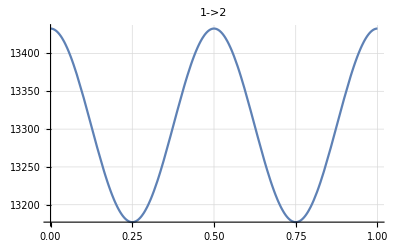
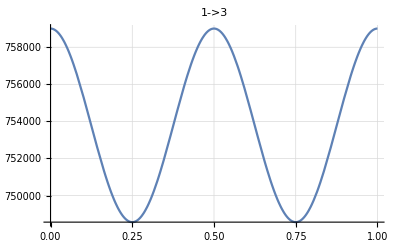
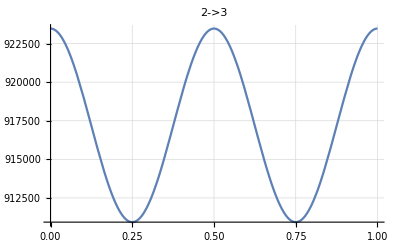
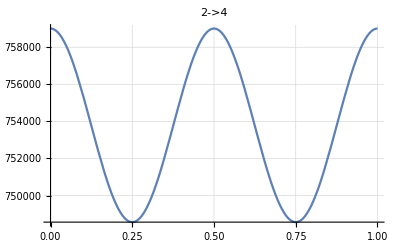
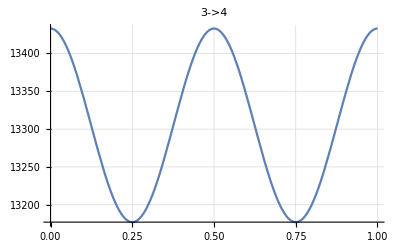

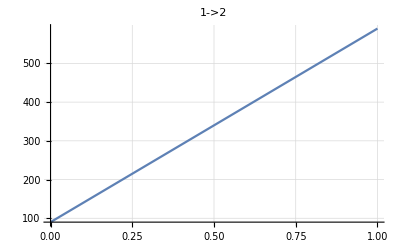
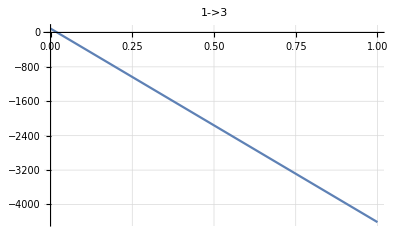
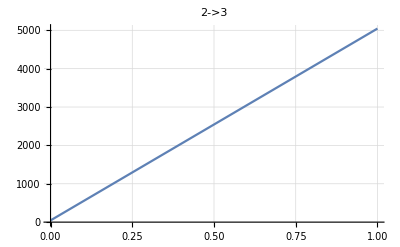

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
FFR=MFGEquations["criticalreduced1"][[2]];
FFR = mtrules;
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#,(*PlotRange->{-0.1,2.4},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#(*,PlotRange->{1-0.1,4.7}*),GridLines->Automatic]&/@MFGEquations["BEL"]
```

#### Graphs for critical congestion and different Hamiltonians on edges

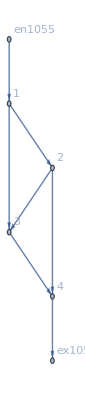

```mathematica
MFGEquations["FG"]
```

```mathematica
(*the hamiltonian that we define a posteriori needs to be consistent with the algebraic system provided by the current method.*)
```

```mathematica
H=Function[{x,p,m,edge},
Which[edge === 1->2 || edge === 3->4,
p^2/(2 m)-20-g[m],
edge === 1->3||edge===2->4,
p^2/(2 m)+20-g[m],
edge === 2->3,
p^2/(2 m)+20-g[m],
True,
40
]
];
```

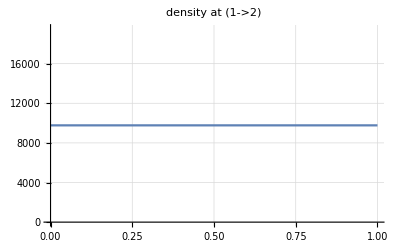
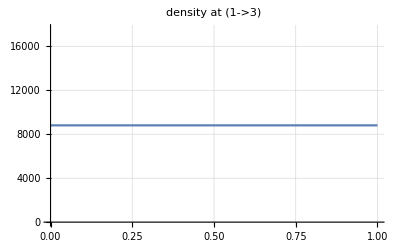
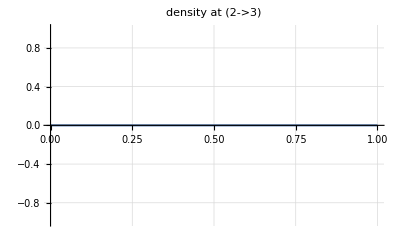
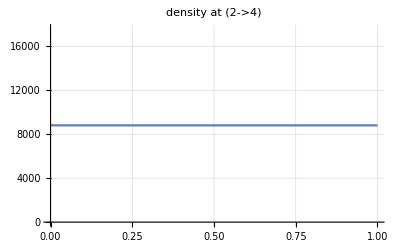
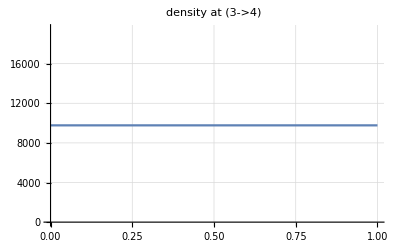

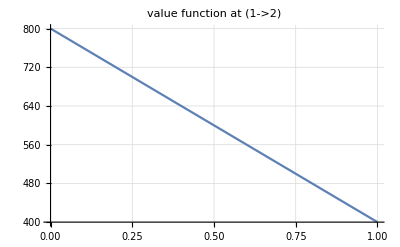
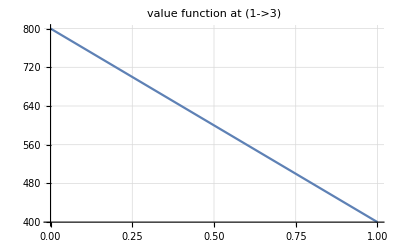
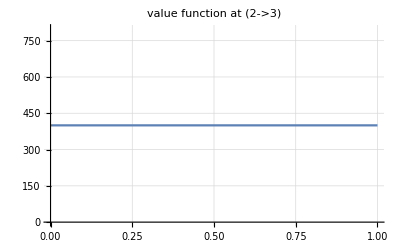

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"density at " #,(*PlotRange->{-0.3,160},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at " #,(*PlotRange->{15-0.1,100},*)GridLines->Automatic]&/@MFGEquations["BEL"]
```

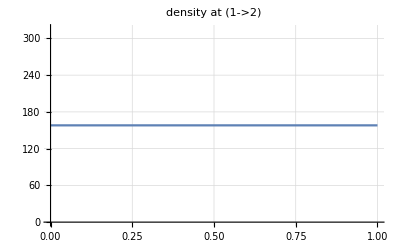
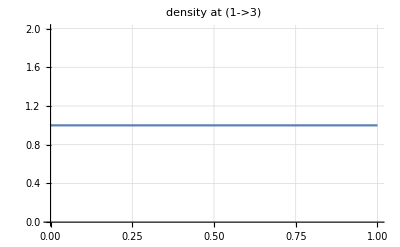
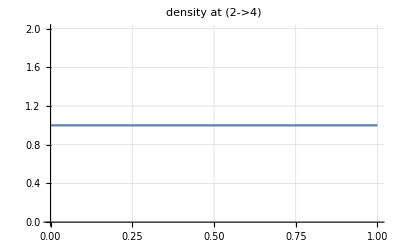
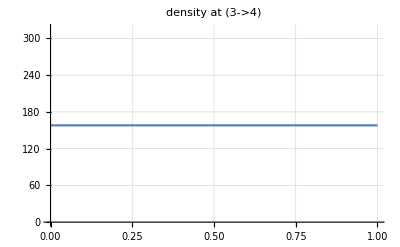
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

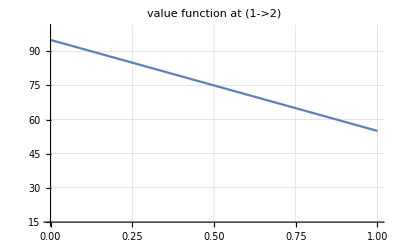
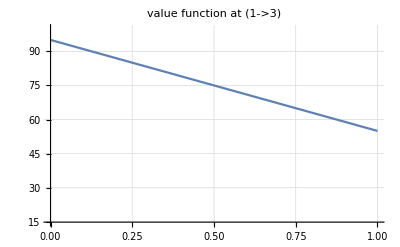
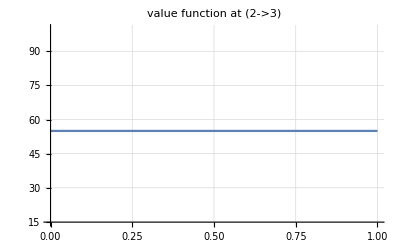
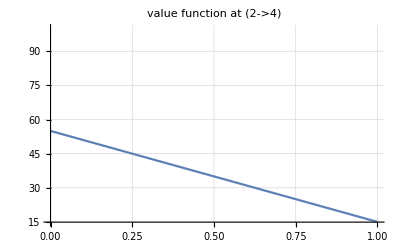
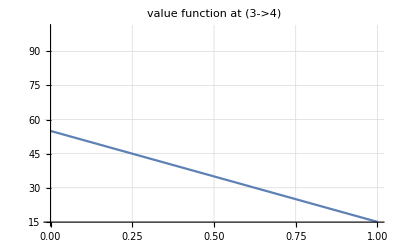

```mathematica
H=Function[{x,p,m,edge},
Which[edge === 1->2 || edge === 3->4,
p^2/(2 m)-g[m],
edge === 1->3||edge===2->4,
p^2/(2 m)g[m],
edge === 2->3,
p^2/(2 m)-100-m,
True,
40
]
];
(*Don't forget to change the Range!*)
alpha =1;
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"density at " #,(*PlotRange->{-0.3,160},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at " #,PlotRange->{15-0.1,100},GridLines->Automatic]&/@MFGEquations["BEL"]
```

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.16139×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.16139×10^-16

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→19.6805,u1096→19.6805,u1097→17.3402,u1098→17.3402,u1099→17.3402,u1100→15.,u1101→19.6805,u1102→17.3402,u1103→17.3402,u1104→17.3402,u1105→15.,u1106→15.,u1107→15.,u1108→19.6805|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j557-j564-u595+u602==38.3971&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.272367

FRX1: nonlinear: 
j557-j564-u595+u602==52.7699&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0925456

FRX1: nonlinear: 
j557-j564-u595+u602==58.1516&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0334946

FRX1: nonlinear: 
j557-j564-u595+u602==60.1668&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0123877

FRX1: nonlinear: 
j557-j564-u595+u602==60.9215&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00461755

FRX1: nonlinear: 
j557-j564-u595+u602==61.2041&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00172622

FRX1: nonlinear: 
j557-j564-u595+u602==61.3099&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000646026

FRX1: nonlinear: 
j557-j564-u595+u602==61.3496&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000241869

FRX1: nonlinear: 
j557-j564-u595+u602==61.3644&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000905682

FRX1: nonlinear: 
j557-j564-u595+u602==61.37&&j558-j565-u596+u603==0&&j559-j566-u597+u604==0&&j560-j567-u598+u605==0&&j561-j568-u599+u606==0

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000339154

<|j557→63.0137,j558→16.9863,j559→15.3425,j560→47.6712,j561→32.3288,j562→80,j563→80,j564→0.,j565→0,j566→0,j567→0,j568→0,j569→0,j570→0,jt571→0.,jt572→0,jt573→0,jt574→0,jt575→63.0137,jt576→16.9863,jt577→15.3425,jt578→47.6712,jt579→0.,jt580→0.,jt581→0,jt582→0,jt583→0,jt584→16.9863,jt585→0,jt586→15.3425,jt587→0,jt588→0,jt589→0,jt590→47.6712,jt591→0,jt592→32.3288,jt593→0,jt594→0,u595→64.315,u596→64.315,u597→62.6712,u598→62.6712,u599→47.3288,u600→15,u601→64.315,u602→62.6712,u603→47.3288,u604→47.3288,u605→15.,u606→15.,u607→15,u608→64.315|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.42094×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.42094×10^-17

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→23.1887,u1096→23.1887,u1097→19.0944,u1098→19.0944,u1099→19.0944,u1100→15.,u1101→23.1887,u1102→19.0944,u1103→19.0944,u1104→19.0944,u1105→15.,u1106→15.,u1107→15.,u1108→23.1887|>

FRX1: nonlinear: 
j13-j20-u51+u58==-0.331444&&j14-j21-u52+u59==3.45866&&j15-j22-u53+u60==0&&j16-j23-u54+u61==3.45866&&j17-j24-u55+u62==-0.331444

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.319315

FRX1: nonlinear: 
j13-j20-u51+u58==-0.411665&&j14-j21-u52+u59==4.27795&&j15-j22-u53+u60==-1.63858&&j16-j23-u54+u61==4.27795&&j17-j24-u55+u62==-0.411665

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.182181

FRX1: nonlinear: 
j13-j20-u51+u58==-0.439187&&j14-j21-u52+u59==4.8266&&j15-j22-u53+u60==-2.73589&&j16-j23-u54+u61==4.8266&&j17-j24-u55+u62==-0.439187

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.108911

FRX1: nonlinear: 
j13-j20-u51+u58==-0.442215&&j14-j21-u52+u59==5.18835&&j15-j22-u53+u60==-3.45938&&j16-j23-u54+u61==5.18835&&j17-j24-u55+u62==-0.442215

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0666991

FRX1: nonlinear: 
j13-j20-u51+u58==-0.436109&&j14-j21-u52+u59==5.4236&&j15-j22-u53+u60==-3.92988&&j16-j23-u54+u61==5.4236&&j17-j24-u55+u62==-0.436109

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0413245

FRX1: nonlinear: 
j13-j20-u51+u58==-0.428181&&j14-j21-u52+u59==5.57484&&j15-j22-u53+u60==-4.23235&&j16-j23-u54+u61==5.57484&&j17-j24-u55+u62==-0.428181

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0257364

FRX1: nonlinear: 
j13-j20-u51+u58==-0.421269&&j14-j21-u52+u59==5.6712&&j15-j22-u53+u60==-4.42508&&j16-j23-u54+u61==5.6712&&j17-j24-u55+u62==-0.421269

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0160623

FRX1: nonlinear: 
j13-j20-u51+u58==-0.416075&&j14-j21-u52+u59==5.7322&&j15-j22-u53+u60==-4.54708&&j16-j23-u54+u61==5.7322&&j17-j24-u55+u62==-0.416075

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0100323

FRX1: nonlinear: 
j13-j20-u51+u58==-0.412455&&j14-j21-u52+u59==5.77063&&j15-j22-u53+u60==-4.62395&&j16-j23-u54+u61==5.77063&&j17-j24-u55+u62==-0.412455

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0062674

FRX1: nonlinear: 
j13-j20-u51+u58==-0.410039&&j14-j21-u52+u59==5.79477&&j15-j22-u53+u60==-4.67223&&j16-j23-u54+u61==5.79477&&j17-j24-u55+u62==-0.410039

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00391545

FRX1: nonlinear: 
j13-j20-u51+u58==-0.408466&&j14-j21-u52+u59==5.80991&&j15-j22-u53+u60==-4.7025&&j16-j23-u54+u61==5.80991&&j17-j24-u55+u62==-0.408466

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00244603

FRX1: nonlinear: 
j13-j20-u51+u58==-0.407459&&j14-j21-u52+u59==5.81938&&j15-j22-u53+u60==-4.72145&&j16-j23-u54+u61==5.81938&&j17-j24-u55+u62==-0.407459

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00152799

FRX1: nonlinear: 
j13-j20-u51+u58==-0.406819&&j14-j21-u52+u59==5.82531&&j15-j22-u53+u60==-4.7333&&j16-j23-u54+u61==5.82531&&j17-j24-u55+u62==-0.406819

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000954478

FRX1: nonlinear: 
j13-j20-u51+u58==-0.406416&&j14-j21-u52+u59==5.82901&&j15-j22-u53+u60==-4.74071&&j16-j23-u54+u61==5.82901&&j17-j24-u55+u62==-0.406416

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000596211

FRX1: nonlinear: 
j13-j20-u51+u58==-0.406162&&j14-j21-u52+u59==5.83133&&j15-j22-u53+u60==-4.74534&&j16-j23-u54+u61==5.83133&&j17-j24-u55+u62==-0.406162

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000372415

FRX1: nonlinear: 
j13-j20-u51+u58==-0.406003&&j14-j21-u52+u59==5.83278&&j15-j22-u53+u60==-4.74823&&j16-j23-u54+u61==5.83278&&j17-j24-u55+u62==-0.406003

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000232621

FRX1: nonlinear: 
j13-j20-u51+u58==-0.405904&&j14-j21-u52+u59==5.83368&&j15-j22-u53+u60==-4.75004&&j16-j23-u54+u61==5.83368&&j17-j24-u55+u62==-0.405904

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000145301

FRX1: nonlinear: 
j13-j20-u51+u58==-0.405842&&j14-j21-u52+u59==5.83424&&j15-j22-u53+u60==-4.75117&&j16-j23-u54+u61==5.83424&&j17-j24-u55+u62==-0.405842

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000907578

FRX1: nonlinear: 
j13-j20-u51+u58==-0.405803&&j14-j21-u52+u59==5.8346&&j15-j22-u53+u60==-4.75188&&j16-j23-u54+u61==5.8346&&j17-j24-u55+u62==-0.405803

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000566891

FRX1: nonlinear: 
j13-j20-u51+u58==-0.405779&&j14-j21-u52+u59==5.83482&&j15-j22-u53+u60==-4.75232&&j16-j23-u54+u61==5.83482&&j17-j24-u55+u62==-0.405779

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000354091

FRX1: nonlinear: 
j13-j20-u51+u58==-0.405763&&j14-j21-u52+u59==5.83495&&j15-j22-u53+u60==-4.75259&&j16-j23-u54+u61==5.83495&&j17-j24-u55+u62==-0.405763

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000221171

FRX1: nonlinear: 
j13-j20-u51+u58==-0.405754&&j14-j21-u52+u59==5.83504&&j15-j22-u53+u60==-4.75276&&j16-j23-u54+u61==5.83504&&j17-j24-u55+u62==-0.405754

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000138147

FRX1: nonlinear: 
j13-j20-u51+u58==-0.405748&&j14-j21-u52+u59==5.83509&&j15-j22-u53+u60==-4.75287&&j16-j23-u54+u61==5.83509&&j17-j24-u55+u62==-0.405748

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 8.62893×10^-6

FRX1: nonlinear: 
j13-j20-u51+u58==-0.405744&&j14-j21-u52+u59==5.83513&&j15-j22-u53+u60==-4.75294&&j16-j23-u54+u61==5.83513&&j17-j24-u55+u62==-0.405744

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.38977×10^-6

FRX1: nonlinear: 
j13-j20-u51+u58==-0.405742&&j14-j21-u52+u59==5.83515&&j15-j22-u53+u60==-4.75298&&j16-j23-u54+u61==5.83515&&j17-j24-u55+u62==-0.405742

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.36654×10^-6

FRX1: nonlinear: 
j13-j20-u51+u58==-0.40574&&j14-j21-u52+u59==5.83516&&j15-j22-u53+u60==-4.75301&&j16-j23-u54+u61==5.83516&&j17-j24-u55+u62==-0.40574

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.1028×10^-6

FRX1: nonlinear: 
j13-j20-u51+u58==-0.40574&&j14-j21-u52+u59==5.83517&&j15-j22-u53+u60==-4.75302&&j16-j23-u54+u61==5.83517&&j17-j24-u55+u62==-0.40574

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.31344×10^-6

FRX1: nonlinear: 
j13-j20-u51+u58==-0.405739&&j14-j21-u52+u59==5.83518&&j15-j22-u53+u60==-4.75303&&j16-j23-u54+u61==5.83518&&j17-j24-u55+u62==-0.405739

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 8.20398×10^-7

FRX1: nonlinear: 
j13-j20-u51+u58==-0.405739&&j14-j21-u52+u59==5.83518&&j15-j22-u53+u60==-4.75304&&j16-j23-u54+u61==5.83518&&j17-j24-u55+u62==-0.405739

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.12434×10^-7

FRX1: nonlinear: 
j13-j20-u51+u58==-0.405738&&j14-j21-u52+u59==5.83518&&j15-j22-u53+u60==-4.75304&&j16-j23-u54+u61==5.83518&&j17-j24-u55+u62==-0.405738

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.20075×10^-7

FRX1: nonlinear: 
j13-j20-u51+u58==-0.405738&&j14-j21-u52+u59==5.83518&&j15-j22-u53+u60==-4.75305&&j16-j23-u54+u61==5.83518&&j17-j24-u55+u62==-0.405738

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.99924×10^-7

FRX1: nonlinear: 
j13-j20-u51+u58==-0.405738&&j14-j21-u52+u59==5.83518&&j15-j22-u53+u60==-4.75305&&j16-j23-u54+u61==5.83518&&j17-j24-u55+u62==-0.405738

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.24876×10^-7

FRX1: nonlinear: 
j13-j20-u51+u58==-0.405738&&j14-j21-u52+u59==5.83518&&j15-j22-u53+u60==-4.75305&&j16-j23-u54+u61==5.83518&&j17-j24-u55+u62==-0.405738

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.79996×10^-8

FRX1: nonlinear: 
j13-j20-u51+u58==-0.405738&&j14-j21-u52+u59==5.83518&&j15-j22-u53+u60==-4.75305&&j16-j23-u54+u61==5.83518&&j17-j24-u55+u62==-0.405738

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.87198×10^-8

<|j13→1.25151,j14→6.74849,j15→0.,j16→6.74849,j17→1.25151,j18→8,j19→8,j20→0.,j21→0,j22→5.49698,j23→0,j24→0,j25→0,j26→0,jt27→0.,jt28→0,jt29→0,jt30→0,jt31→1.25151,jt32→6.74849,jt33→0.,jt34→1.25151,jt35→0.,jt36→5.49698,jt37→0,jt38→0,jt39→5.49698,jt40→1.25151,jt41→0,jt42→0.,jt43→0,jt44→0,jt45→0,jt46→6.74849,jt47→0,jt48→1.25151,jt49→0,jt50→0,u51→2.57056,u52→2.57056,u53→0.913309,u54→0.913309,u55→1.65725,u56→0,u57→2.57056,u58→0.913309,u59→1.65725,u60→1.65725,u61→0.,u62→0.,u63→0,u64→2.57056|>

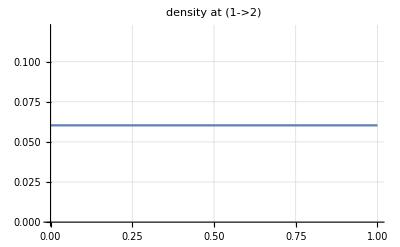
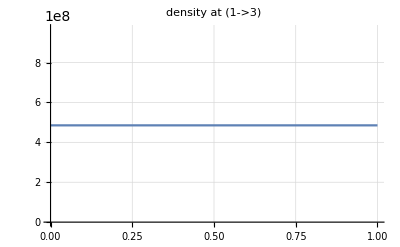
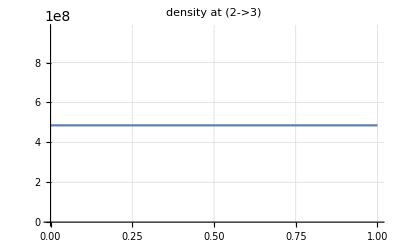
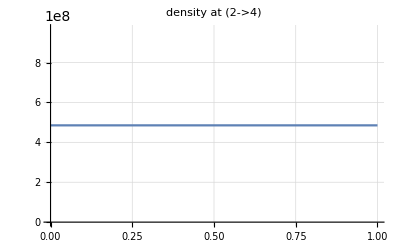
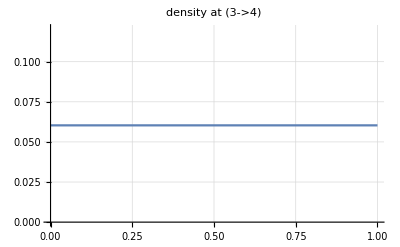

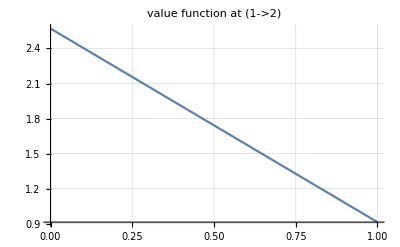
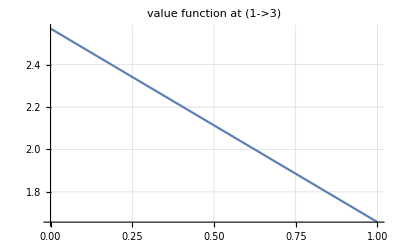
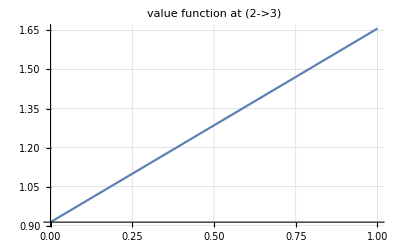

```mathematica
alpha = 0.9;
H=Function[{x,p,m,edge},
Which[edge === 1->2 || edge === 3->4,
p^2/(2 m^alpha)-20-g[m],
edge === 1->3||edge===2->4,
p^2/(2 m^alpha)+20-g[m],
edge === 2->3,
p^2/(2 m^alpha)+20-g[m],
True,
40
]
];
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],100,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"density at " #,(*PlotRange->{-0.3,160},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at " #,(*PlotRange->{15-0.1,100},*)GridLines->Automatic]&/@MFGEquations["BEL"]
```

FRX1: nonlinear: 
j883-j890-u921+u928==0.574963&&j884-j891-u922+u929==0.574963&&j885-j892-u923+u930==0&&j886-j893-u924+u931==0.574963&&j887-j894-u925+u932==0.574963

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.72378×10^-16

FRX1: nonlinear: 
j883-j890-u921+u928==0.574963&&j884-j891-u922+u929==0.574963&&j885-j892-u923+u930==0&&j886-j893-u924+u931==0.574963&&j887-j894-u925+u932==0.574963

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.72378×10^-16

<|j883→4.,j884→4.,j885→0.,j886→4.,j887→4.,j888→8,j889→8,j890→0.,j891→0,j892→0,j893→0,j894→0,j895→0,j896→0,jt897→0.,jt898→0,jt899→0,jt900→0,jt901→4.,jt902→4.,jt903→0.,jt904→4.,jt905→0.,jt906→0.,jt907→0,jt908→0,jt909→0,jt910→4.,jt911→0,jt912→0.,jt913→0,jt914→0,jt915→0,jt916→4.,jt917→0,jt918→4.,jt919→0,jt920→0,u921→6.85007,u922→6.85007,u923→3.42504,u924→3.42504,u925→3.42504,u926→0,u927→6.85007,u928→3.42504,u929→3.42504,u930→3.42504,u931→0.,u932→0.,u933→0,u934→6.85007|>

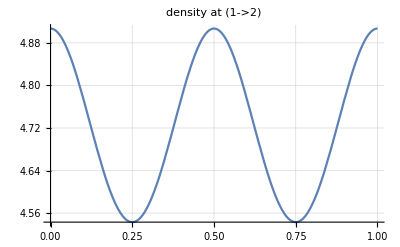
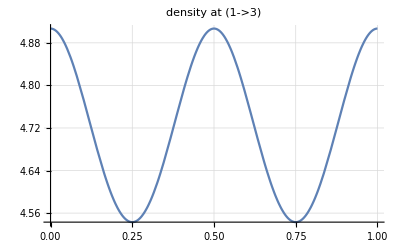
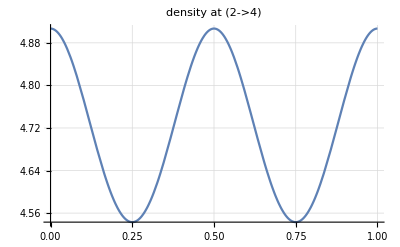
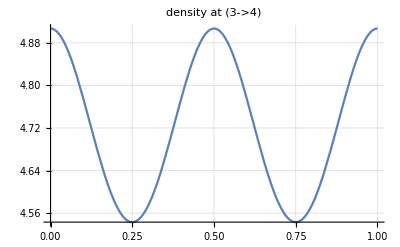
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

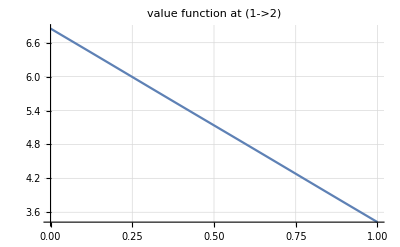
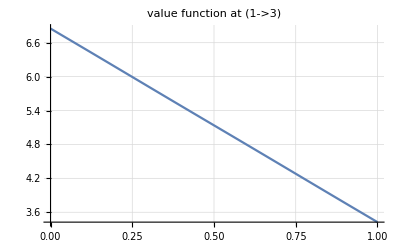
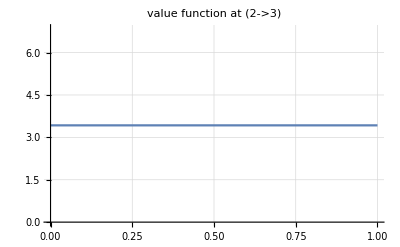
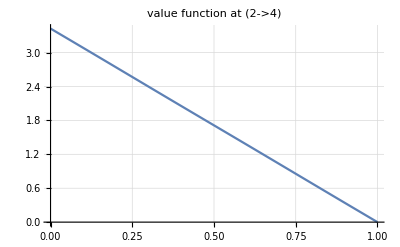
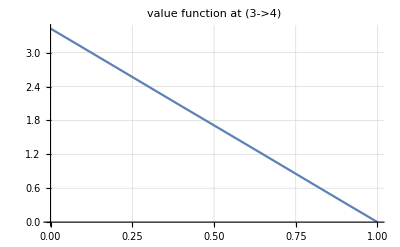

```mathematica
alpha = 0.9;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"]
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"density at " #,(*PlotRange->{-0.3,160},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at " #,(*PlotRange->{15-0.1,100},*)GridLines->Automatic]&/@MFGEquations["BEL"]
```

```mathematica
alpha = 1.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j13-j20-u51+u58==-0.766268&&j14-j21-u52+u59==-0.766268&&j15-j22-u53+u60==0&&j16-j23-u54+u61==-0.766268&&j17-j24-u55+u62==-0.766268

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.1591×10^-15

FRX1: nonlinear: 
j13-j20-u51+u58==-0.766268&&j14-j21-u52+u59==-0.766268&&j15-j22-u53+u60==0&&j16-j23-u54+u61==-0.766268&&j17-j24-u55+u62==-0.766268

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.1591×10^-15

<|j13→4.,j14→4.,j15→0.,j16→4.,j17→4.,j18→8,j19→8,j20→0.,j21→0,j22→0,j23→0,j24→0,j25→0,j26→0,jt27→0.,jt28→0,jt29→0,jt30→0,jt31→4.,jt32→4.,jt33→0.,jt34→4.,jt35→0.,jt36→0.,jt37→0,jt38→0,jt39→0,jt40→4.,jt41→0,jt42→0.,jt43→0,jt44→0,jt45→0,jt46→4.,jt47→0,jt48→4.,jt49→0,jt50→0,u51→9.53254,u52→9.53254,u53→4.76627,u54→4.76627,u55→4.76627,u56→0,u57→9.53254,u58→4.76627,u59→4.76627,u60→4.76627,u61→0.,u62→0.,u63→0,u64→9.53254|>

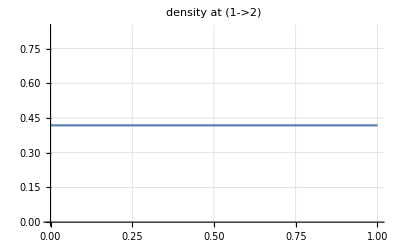
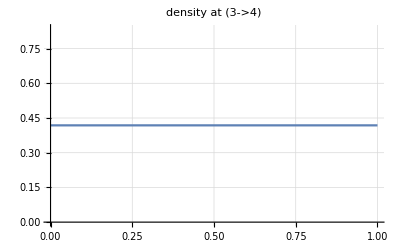
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

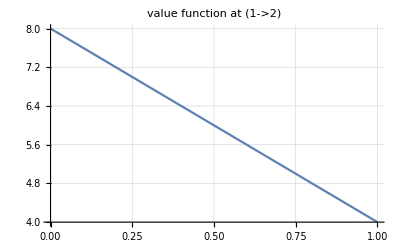
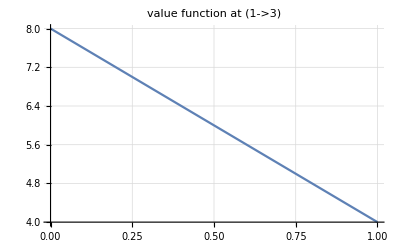
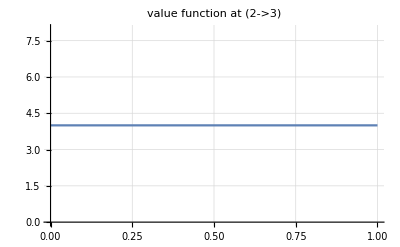
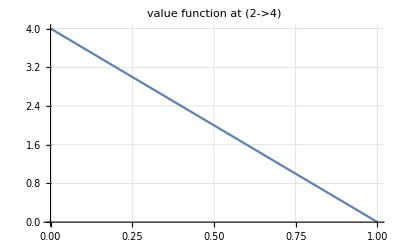
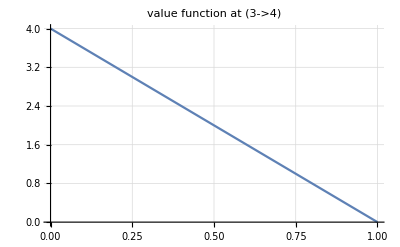

```mathematica
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"density at " #,(*PlotRange->{-0.3,160},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at " #,(*PlotRange->{15-0.1,100},*)GridLines->Automatic]&/@MFGEquations["BEL"]
```

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j13-j20-u51+u58==0.774623&&j14-j21-u52+u59==-214.393&&j15-j22-u53+u60==0&&j16-j23-u54+u61==-214.393&&j17-j24-u55+u62==0.774623

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.02474

FRX1: nonlinear: 
j13-j20-u51+u58==-107.032&&j14-j21-u52+u59==2668.83&&j15-j22-u53+u60==-5767.05&&j16-j23-u54+u61==2668.83&&j17-j24-u55+u62==-107.032

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.02182

FRX1: nonlinear: 
j13-j20-u51+u58==32170.1&&j14-j21-u52+u59==-119858.&&j15-j22-u53+u60==259912.&&j16-j23-u54+u61==-119858.&&j17-j24-u55+u62==32170.1

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00553

FRX1: nonlinear: 
j13-j20-u51+u58==-1.07327×10^7&&j14-j21-u52+u59==1.78091×10^7&&j15-j22-u53+u60==-4.77028×10^7&&j16-j23-u54+u61==1.78091×10^7&&j17-j24-u55+u62==-1.07327×10^7

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.0005

FRX1: nonlinear: 
j13-j20-u51+u58==2.55609×10^10&&j14-j21-u52+u59==-3.42117×10^10&&j15-j22-u53+u60==9.46555×10^10&&j16-j23-u54+u61==-3.42117×10^10&&j17-j24-u55+u62==2.55609×10^10

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00001

$Aborted

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j13-j20-u51+u58==2.25524&&j14-j21-u52+u59==-88117.9&&j15-j22-u53+u60==0&&j16-j23-u54+u61==-88117.9&&j17-j24-u55+u62==2.25524

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: nonlinear: 
j13-j20-u51+u58==-1.05371×10^11&&j14-j21-u52+u59==3.98128×10^11&&j15-j22-u53+u60==-2.69661×10^12&&j16-j23-u54+u61==3.98128×10^11&&j17-j24-u55+u62==-1.05371×10^11

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: nonlinear: 
j13-j20-u51+u58==2.15706×10^33&&j14-j21-u52+u59==-3.2207×10^33&&j15-j22-u53+u60==2.49175×10^34&&j16-j23-u54+u61==-3.2207×10^33&&j17-j24-u55+u62==2.15706×10^33

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

$Aborted

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j13-j20-u51+u58==-346.136&&j14-j21-u52+u59==-346.136&&j15-j22-u53+u60==0&&j16-j23-u54+u61==-346.136&&j17-j24-u55+u62==-346.136

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: nonlinear: 
j13-j20-u51+u58==-346.136&&j14-j21-u52+u59==-346.136&&j15-j22-u53+u60==0&&j16-j23-u54+u61==-346.136&&j17-j24-u55+u62==-346.136

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j13→4.,j14→4.,j15→0.,j16→4.,j17→4.,j18→8,j19→8,j20→0.,j21→0,j22→0,j23→0,j24→0,j25→0,j26→0,jt27→0.,jt28→0,jt29→0,jt30→0,jt31→4.,jt32→4.,jt33→0.,jt34→4.,jt35→0.,jt36→0.,jt37→0,jt38→0,jt39→0,jt40→4.,jt41→0,jt42→0.,jt43→0,jt44→0,jt45→0,jt46→4.,jt47→0,jt48→4.,jt49→0,jt50→0,u51→700.271,u52→700.271,u53→350.136,u54→350.136,u55→350.136,u56→0,u57→700.271,u58→350.136,u59→350.136,u60→350.136,u61→0.,u62→0.,u63→0,u64→700.271|>

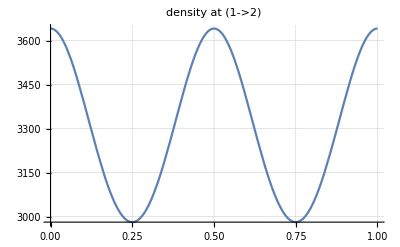
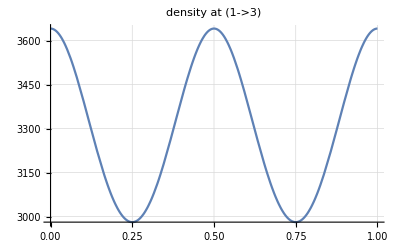
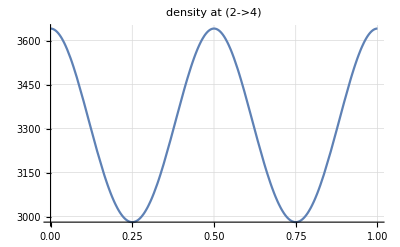
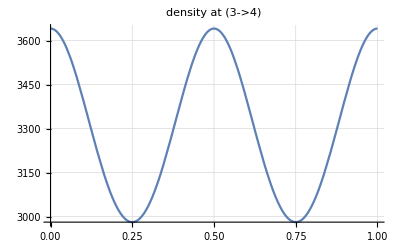
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

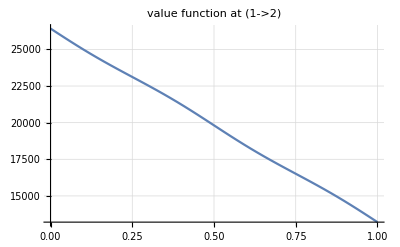
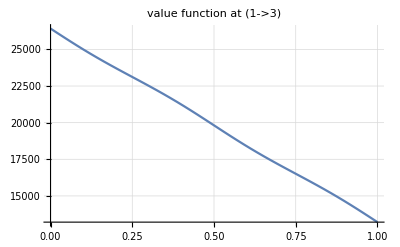
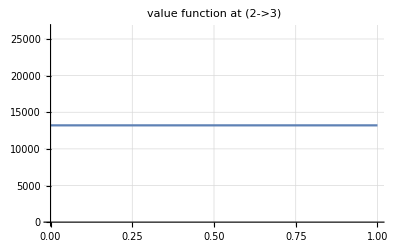
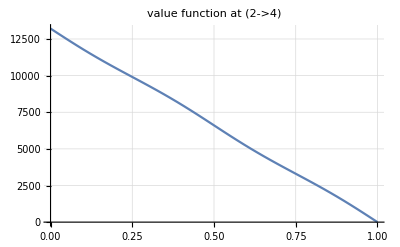
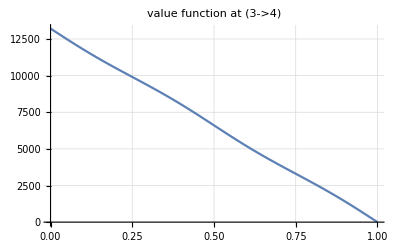

```mathematica
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"density at " #,(*PlotRange->{-0.3,160},*)GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at " #,(*PlotRange->{15-0.1,100},*)GridLines->Automatic]&/@MFGEquations["BEL"]
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: nonlinear: 
j13-j20-u51+u58==-13206.8&&j14-j21-u52+u59==-13206.8&&j15-j22-u53+u60==0&&j16-j23-u54+u61==-13206.8&&j17-j24-u55+u62==-13206.8

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: nonlinear: 
j13-j20-u51+u58==-13206.8&&j14-j21-u52+u59==-13206.8&&j15-j22-u53+u60==0&&j16-j23-u54+u61==-13206.8&&j17-j24-u55+u62==-13206.8

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j13→4.,j14→4.,j15→0.,j16→4.,j17→4.,j18→8,j19→8,j20→0.,j21→0,j22→0,j23→0,j24→0,j25→0,j26→0,jt27→0.,jt28→0,jt29→0,jt30→0,jt31→4.,jt32→4.,jt33→0.,jt34→4.,jt35→0.,jt36→0.,jt37→0,jt38→0,jt39→0,jt40→4.,jt41→0,jt42→0.,jt43→0,jt44→0,jt45→0,jt46→4.,jt47→0,jt48→4.,jt49→0,jt50→0,u51→26421.7,u52→26421.7,u53→13210.8,u54→13210.8,u55→13210.8,u56→0,u57→26421.7,u58→13210.8,u59→13210.8,u60→13210.8,u61→0.,u62→0.,u63→0,u64→26421.7|>